```mathematica
Needs["QuantumUtils`"]
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

Macro for exporting figures to file:

```mathematica
$doExport=False;
exportme[filename_][fig_]:=(SetDirectory[NotebookDirectory[]];If[$doExport,Export[filename,fig]];fig)
```

### Parameters

Set up the parameter values to be used by default.

```mathematica
$Assumptions=k>0&&γeg>γes>γsg>γ01>0&&Δt>0;
```

```mathematica
params[r___Rule]:=Join[{r},{
k->0.3,
γeg->77,
γes-> 30,
γsg-> 3,
γ01->0.5,
Δt->0.3,
Γ->5000/10^6,
η->0.001
}]
```

### Lindblad Operators and Hamiltonians

Set up the state vectors, Lindblad operators, Hamiltonians, and super generators.

```mathematica
{sgp,sgz,sgm,sep,sez,sem,ss}=IdentityMatrix[7];
```

```mathematica
L[1]=Sqrt[γeg](OuterProduct[sgp,sep]+OuterProduct[sgz,sez]+OuterProduct[sgm,sem]);
L[2]=Sqrt[k*γeg](OuterProduct[sep,sgp]+OuterProduct[sez,sgz]+OuterProduct[sem,sgm]);

L[3]=Sqrt[γes/2]OuterProduct[ss,sep];
L[4]=Sqrt[γes/2]OuterProduct[ss,sem];
L[5]=Sqrt[ γsg/3]OuterProduct[sgp,ss];
L[6]=Sqrt[γsg/3]OuterProduct[sgz,ss];
L[7]=Sqrt[ γsg/3]OuterProduct[sgm,ss];

L[8]=Sqrt[γ01/4]OuterProduct[sgp,sez];
L[9]=Sqrt[γ01/4]OuterProduct[sgm,sez];
L[10]=Sqrt[γ01/4]OuterProduct[sgz,sep];
L[11]=Sqrt[γ01/4]OuterProduct[sgz,sem];
```

```mathematica
H=Δg (Projector[sgp,sgm])+Δe (Projector[sep,sem]);
Sx=(OuterProduct[sgp,sgz]+OuterProduct[sgm,sgz]+OuterProduct[sgz,sgm]+OuterProduct[sgz,sgp])/Sqrt[2];
```

```mathematica
LSim=LindbladForm[0*H,Table[L[n]/.k->0,{n,11}]];
LControl=First@LindbladDissipator[L[2]];
```

### Rate Matrix Steady State

Rate matrix:

```mathematica
R=({{-k γeg, 0, γeg, γ01/2, γsg/3}, {0, -k γeg, γ01/2, γeg, 2γsg/3}, {k γeg, 0, -γeg-γ01/2, 0, 0}, {0, k γeg, 0, -γeg-γes-γ01/2, 0}, {0, 0, 0, γes, -γsg}});
```

First look at the eigensystem with the laser off, which is easy to analyze:

```mathematica
Eigensystem[R/.{k->0},5]//FullSimplify//EigensystemForm
```

0 | 0 | -γ01/2-γeg | -γ01/2-γeg-γes | -γsg
↓ | ↓ | ↓ | ↓ | ↓
(0
1
0
0
0) | (1
0
0
0
0) | (-(2 γeg)/(γ01+2 γeg)
-γ01/(γ01+2 γeg)
1
0
0) | ((3 γ01-(2 (3 γ01+2 γes) γsg)/(γ01+2 (γeg+γes)))/(6 γes)
(3 γeg-(2 (3 γeg+2 γes) γsg)/(γ01+2 (γeg+γes)))/(3 γes)
0
-(γ01+2 (γeg+γes-γsg))/(2 γes)
1) | (-1/3
-2/3
0
0
1)

With the laser on we can look at the null space:

```mathematica
Eigensystem[R,1]//FullSimplify//EigensystemForm
```

0
↓
(((γ01+2 γeg) (3 γ01+2 γes) γsg)/(6 k γ01 γeg γes)
((γ01+2 (γeg+γes)) γsg)/(2 k γeg γes)
(2 γsg)/(3 γ01)+γsg/γes
γsg/γes
1)

Normalize this vector and consider a taylor series of γ01 about 0:

```mathematica
v0=({{((γ01+2 γeg) (3 γ01+2 γes) γsg)/(6 k γ01 γeg γes)}, {((γ01+2 (γeg+γes)) γsg)/(2 k γeg γes)}, {(2 γsg)/(3 γ01)+γsg/γes}, {γsg/γes}, {1}})/Total[({{((γ01+2 γeg) (3 γ01+2 γes) γsg)/(6 k γ01 γeg γes)}, {((γ01+2 (γeg+γes)) γsg)/(2 k γeg γes)}, {(2 γsg)/(3 γ01)+γsg/γes}, {γsg/γes}, {1}})]//FullSimplify;
v0p=Series[v0,{γ01,0,1}]//FullSimplify//Normal
```

{1/(1+k)+(γ01 (-3 (γeg+γes) γsg+k (γes γsg-3 γeg (γes+γsg))))/(2 (1+k)^2 γeg γes γsg),(γ01 (3 γeg+3 γes))/(2 γeg γes+2 k γeg γes),k/(1+k)-(k γ01 ((3 γeg+4 γes) γsg+3 k γeg (γes+γsg)))/(2 (1+k)^2 γeg γes γsg),(3 k γ01)/(2 γes+2 k γes),(3 k γ01)/(2 γsg+2 k γsg)}

Plot the steady state of the exact solution as a function of γ01:

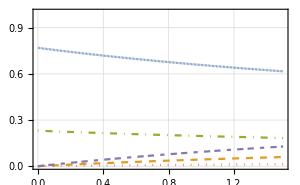

```mathematica
exportme["../fig/null-space-vector.pdf"]@Plot[
Evaluate[v0/.params[k->0.3,γ01->γ]],{γ,0,1.5},
PlotRange->{0,1},
PlotLegends->(MaTeX[#,FontSize->14]&/@{"p_{g,0}","p_{g,1}","p_{e,0}","p_{e,1}","p_s"}),
PlotStyle->{Dashing[0],Dashed,DotDashed,Dotted,Dashing[{.015,0.01,.015}]},
PlotTheme->"Detailed",
PlotLabel->MaTeX["\\text{Components of the Null Space Vector}",FontSize->14],
FrameLabel->{MaTeX["\\gamma_{01}~(\\text{MHz})",FontSize->14],MaTeX["\\text{population}",FontSize->14]},
ImageSize->300,
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}
]
```

### Dynamics

Simulate laser off 1us, laser on 5us, laser off 1us under three initial states.

```mathematica
data1=PulseSim[LSim/.params[],{{{1,0},{5,1},{1,0}},{LControl/.params[k->.3]}},InitialState->Projector[sgz,sgm,sgp]/3,Observables->(Projector@@@{{ss},{sgz},{sgp,sgm},{sez},{sep,sem}}),PollingInterval->0.01];
data2=PulseSim[LSim/.params[],{{{1,0},{5,1},{1,0}},{LControl/.params[k->.3]}},InitialState->Projector[sgz],Observables->(Projector@@@{{ss},{sgz},{sgp,sgm},{sez},{sep,sem}}),PollingInterval->0.01];
data3=PulseSim[LSim/.params[],{{{1,0},{5,1},{1,0}},{LControl/.params[k->.3]}},InitialState->Projector[sgm],Observables->(Projector@@@{{ss},{sgz},{sgp,sgm},{sez},{sep,sem}}),PollingInterval->0.01];
```

Plot the first simulation

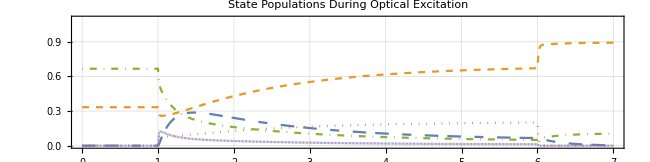

```mathematica
exportme["../fig/state-populations.pdf"]@ListPlot[
Observables[data1,TimeVector->True],
Joined->True,
PlotRange->{0,1.1},
PlotLegends->(MaTeX[#,FontSize->14]&/@{"|s\\rangle","|g,0\\rangle","|g,+1\\rangle,|g,-1\\rangle","|e,0\\rangle","|e,+1\\rangle,|e,-1\\rangle"}),
PlotTheme->"Detailed",
ImageSize->650,
PlotLabel->"State Populations During Optical Excitation",
PlotStyle->{Dashing[{.015,0.01,.015}],Dashed,DotDashed,Dotted,Dashing[0]},
FrameLabel->(MaTeX[#,FontSize->14]&/@{"t~(\\mu s)","\\text{population}"}),
BaseStyle->texStyle,
AspectRatio->1/4]
```

Second simulation (not exported)

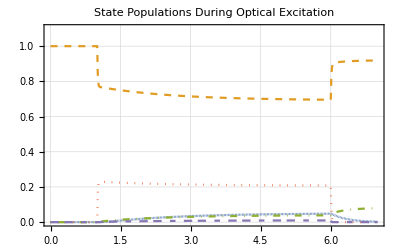

```mathematica
ListPlot[
Observables[data2,TimeVector->True],
Joined->True,
PlotRange->{0,1.1},
PlotLegends->(MaTeX[#,FontSize->14]&/@{"|s\\rangle","|g,0\\rangle","|g,+1\\rangle,|g,-1\\rangle","|e,0\\rangle","|e,+1\\rangle,|e,-1\\rangle"}),
PlotTheme->"Detailed",
ImageSize->400,
PlotLabel->"State Populations During Optical Excitation",
PlotStyle->{Dashing[0],Dashed,DotDashed,Dotted,Dashing[{.015,0.01,.015}]},
FrameLabel->(MaTeX[#,FontSize->14]&/@{"t~(\\mu s)","\\text{population}"}),
BaseStyle->texStyle
]
```

Third simulation (not exported)

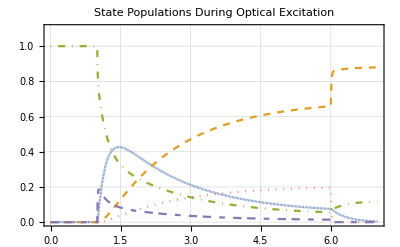

```mathematica
ListPlot[
Observables[data3,TimeVector->True],
Joined->True,
PlotRange->{0,1.1},
PlotLegends->(MaTeX[#,FontSize->14]&/@{"|s\\rangle","|g,0\\rangle","|g,+1\\rangle,|g,-1\\rangle","|e,0\\rangle","|e,+1\\rangle,|e,-1\\rangle"}),
PlotTheme->"Detailed",
ImageSize->400,
PlotLabel->"State Populations During Optical Excitation",
PlotStyle->{Dashing[0],Dashed,DotDashed,Dotted,Dashing[{.015,0.01,.015}]},
FrameLabel->(MaTeX[#,FontSize->14]&/@{"t~(\\mu s)","\\text{population}"}),
BaseStyle->texStyle
]
```

### Measurement Plots

Simulate expected photon emission # vs initial state population, verify it is linear as a sanity check.

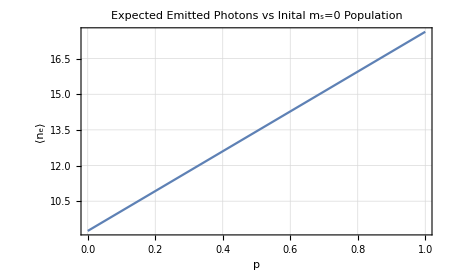

```mathematica
data=Table[{p,(γeg/.params[])*Last@First@Observables@PulseSim[LSim/.params[],{{{.3,1}},{LControl/.params[k->.3]}},InitialState->Projector[Sqrt[p] sgz , Sqrt[1-p]sep],Observables->{Projector[sez,sep,sem]}]},{p,0,1,0.01}];
exportme["../fig/photon-emission-vs-population.pdf"]@ListPlot[data,Joined->True,PlotTheme->"Detailed",FrameLabel->{"p","⟨n_e⟩"},PlotLabel->"Expected Emitted Photons vs Inital m_s=0 Population",ImageSize->450]
```

Define some functions to be used in a bit.

```mathematica
ExpectedPhotons[timeTrace_,p_:params[]]:=Module[{t=Rest@timeTrace[[All,1]],d=Rest@timeTrace[[All,2]],dt},dt=t[[2]]-t[[1]];{t,(Γ/.p) t+((η γeg) /.p)Accumulate[d]dt}ᵀ]
CRBTrace[m0_,m1_,Te_,p_:params[]]:=Module[{e0=ExpectedPhotons[m0,p],e1=ExpectedPhotons[m1,p],t=Rest@m0[[All,1]]},
{t,Sqrt[(Te+3t)2 e0[[All,2]]/((e0-e1)[[All,2]])^2]}ᵀ]
CRBMin[m0_,m1_,Te_,p_:params[]]:=First@MinimalBy[CRBTrace[m0,m1,Te,p],Last]
CRBBestTime[m0_,m1_,Tes_List,p_:params[]]:={Tes+0.01,First[CRBMin[m0,m1,#,p]]&/@Tes}ᵀ
CRBBestValue[m0_,m1_,Tes_List,p_:params[]]:={Tes+0.01,Last[CRBMin[m0,m1,#,p]]&/@Tes}ᵀ
CRBFixedValue[m0_,m1_,Δt_,Tes_List,p_:params[]]:={Tes+0.01,Interpolation[CRBTrace[m0,m1,#,p]][Δt]&/@Tes}ᵀ
```

```mathematica
TwoAxisListPlot[{f_,g_},legend_,opts___]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks,xticks,dashing={{Dashing[1]},{Dashed,DotDashed}},dash},
dash[{n_}]:={Thick,ColorData[1][n],#}&/@dashing[[n]];
{fgraph,ggraph}=MapIndexed[ListLogLinearPlot[#,Axes->True,PlotStyle->dash[#2],opts]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};
fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[Legended[fgraph,legend],ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}}]]
```

As a reminder, the CRB formula is:

```mathematica
((p+1)(p+2)α+p(p-1)β)/(α-β)^2
```

Simulate turning a laser on for 4us with both the initial states ms=0, and ms=+1

```mathematica
data=First@Observables[PulseSim[LSim/.params[],{{{4,1}},{LControl/.params[k->0.5]}},InitialState->Projector[Sqrt[#] sgz , Sqrt[1-#]sgp],Observables->{Projector[sez,sep,sem]},PollingInterval->0.001],TimeVector->True]&/@{1,0};
```

Format and plot results:

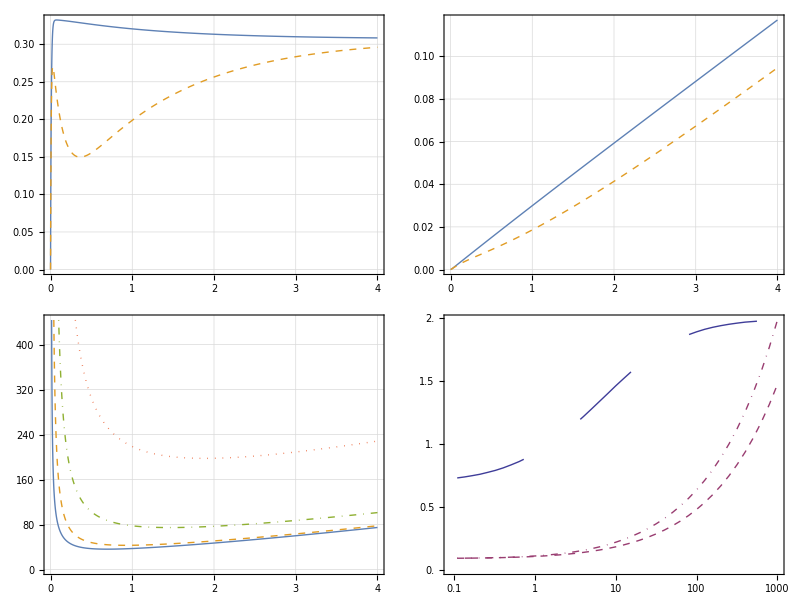

```mathematica
exportme["../fig/opt-measurement.pdf"]@Grid[{{
ListPlot[data,Joined->True,PlotTheme->"Detailed",BaseStyle->texStyle,PlotLabel->MaTeX@"\\text{(a) Excited state population during measurement}",FrameLabel->MaTeX/@{"\\Delta t~(\\mu s)",""},ImageSize->400,PlotLegends->Placed[LineLegend[MaTeX/@{"m_s=0","m_s=1"}],{Right,Bottom}],PlotStyle->{{Thick},{Thick,Dashed}}],
ListPlot[ExpectedPhotons/@data,Joined->True,PlotTheme->"Detailed",BaseStyle->texStyle,PlotLabel->MaTeX@"\\text{(b) Expected photon detections vs. measurement time}",FrameLabel->MaTeX/@{"\\Delta t~(\\mu s)","\\mathbb{E}[n_d]"},ImageSize->425,PlotLegends->Placed[LineLegend[MaTeX/@{"\\overline{\\alpha}(\\Delta t);~m_s=0","\\overline{\\beta}(\\Delta t);~m_s=1"}],{Right,Bottom}],PlotStyle->{{Thick},{Thick,Dashed}}]
},{
ListPlot[CRBTrace[Sequence@@data,#]&/@{0,1,10,100},Joined->True,PlotTheme->"Detailed",BaseStyle->texStyle,PlotLabel->MaTeX@"\\text{(c) }\\sqrt{\\text{CRB / MHz}}",FrameLabel->MaTeX/@{"\\Delta t~(\\mu s)","\\sqrt{\\text{CRB / MHz}}"},ImageSize->400,PlotLegends->Placed[LineLegend[MaTeX["T_e="<>ToString[#]<>"\\mu s"]&/@{0,1,10,100}],{Right,Top}],PlotStyle->{{Thick},{Thick,Dashed},{Thick,DotDashed},{Thick,Dotted}}],
TwoAxisListPlot[{
CRBBestTime[Sequence@@data,10^Range[-1,3,0.1]],
{CRBBestValue[Sequence@@data,10^Range[-1,3,0.1]],
CRBFixedValue[Sequence@@data,0.65,10^Range[-1,3,0.1]]}},
Placed[LineLegend[{Directive[ColorData[1][2],Dashed],Directive[DotDashed,ColorData[1][2]]},MaTeX/@{"\\Delta t_{\\text{opt}}","\\Delta t=0.65\\mu s"}],{0.22,0.85},Identity],
{PlotTheme->"Detailed",PlotRange->All,Joined->True,ImageSize->460,FrameLabel->{MaTeX/@{"\\Delta t_{\\text{opt}}~(\\mu s)","\\sqrt{\\text{CRB / MHz}}"},MaTeX/@{"T_e~(\\mu s)","\\text{(d) Optimal Measurment}"}},BaseStyle->texStyle,ImagePadding->{{60,Automatic},{Automatic,Automatic}}}]
}},Frame->None]
```

Test dependence on laser power:

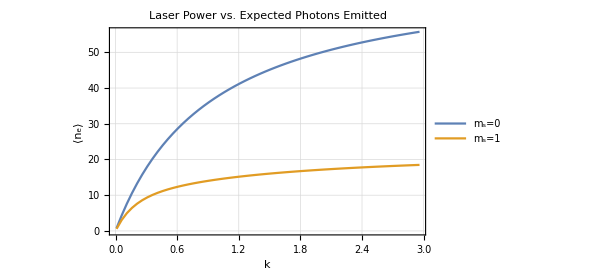
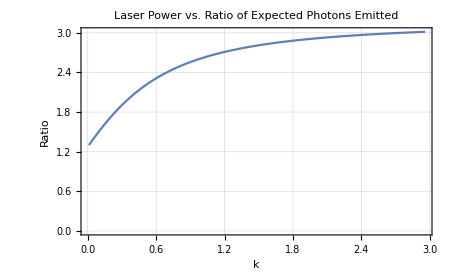

```mathematica
data=Table[{{kk,#/.p->1},{kk,#/.p->0},{kk,(#/.p->1)/(#/.p->0)}}&[(γeg/.params[])*Last@First@Observables@PulseSim[LSim/.params[],{{{.3,1}},{LControl/.params[k->kk]}},InitialState->Projector[Sqrt[p] sgz , Sqrt[1-p]sep],Observables->{Projector[sez,sep,sem]}]],
{kk,0.01,3,0.05}
]ᵀ;
exportme["../fig/photon-emission-laser-dependence.pdf"]@Row[{
ListPlot[data[[{1,2}]],Joined->True,PlotTheme->"Detailed",BaseStyle->texStyle,FrameLabel->{"k","⟨n_e⟩"},PlotLabel->"Laser Power vs. Expected Photons Emitted",ImageSize->450,PlotLegends->Placed[LineLegend[{"m_s=0","m_s=1"}],{Right,Bottom}]],
ListPlot[data[[3]],Joined->True,PlotTheme->"Detailed",FrameLabel->{"k","Ratio"},PlotLabel->"Laser Power vs. Ratio of Expected Photons Emitted",ImageSize->450,PlotRange->All,BaseStyle->texStyle]
}]
```

### Markovian Effects

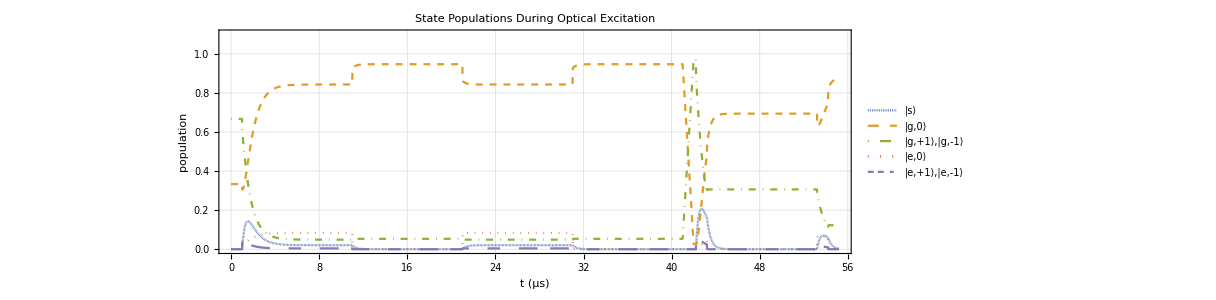

```mathematica
pulse={
{{{1,0},{10,1},{10,0},{10,1},{10,0}},{LControl/.params[k->.1]}},
{BlockMatrix[TP[X],Subscript[𝟙, 5]],1},
{{{.2,0},{1,1},{10,0},{1,1},{1,0}},{LControl/.params[k->.1]}}
};
data=PulseSim[LSim/.params[γ01->1.5,γsg->3],pulse,InitialState->Projector[sgz,sgm,sgp]/3,Observables->(Projector@@@{{ss},{sgz},{sgp,sgm},{sez},{sep,sem}}),PollingInterval->0.02];
ListPlot[
Observables[data,TimeVector->True],
Joined->True,
PlotRange->{0,1.1},
PlotLegends->{"|s⟩","|g,0⟩","|g,+1⟩,|g,-1⟩","|e,0⟩","|e,+1⟩,|e,-1⟩"},
PlotTheme->"Detailed",
ImageSize->900,
PlotLabel->"State Populations During Optical Excitation",
PlotStyle->{Dashing[0],Dashed,DotDashed,Dotted,Dashing[{.015,0.01,.015}]},
FrameLabel->{"t (μs)","population"},
AspectRatio->1/3
]
```